```mathematica
raw=Drop[Import[FileNameJoin[{NotebookDirectory[],"data/out.dat"}], "Table", "FieldSeparators"->{" "}, HeaderLines->1], -1];
```

```mathematica
cdata=Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]]}];
vdata=Transpose[{raw[[All, 12]], raw[[All, 13]], raw[[All, 14]]}];
pdata=raw[[All, 16]];
```

```mathematica
avgv=Mean[Sqrt[vdata[[All, 1]]^2+vdata[[All,2]]^2+vdata[[All, 3]]^2]]
```

0.0572004

```mathematica
maxv=Max[Abs[vdata]]
```

0.274658

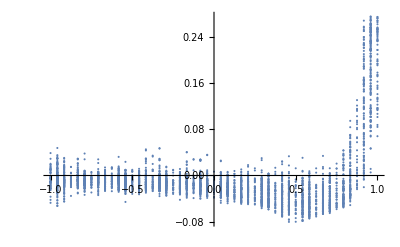

```mathematica
ListPlot[Transpose[{raw[[All, 9]], raw[[All, 12]]}], PlotRange->All]
```

```mathematica
l=Abs[Max[Flatten[cdata]]-Min[Flatten[cdata]]]
```

2.

```mathematica
ren=avgv*l/0.000890
```

128.54

```mathematica
sw=0.01;
ew=1.0;
```

```mathematica
slice=Select[raw,(-sw<#[[8]]/l<sw&&#[[9]]/l+0.5<=1(*&&#[[9]]/l+0.5>ew/l*))&];
```

```mathematica
vs=(Max[raw[[All, 12]]]*1+1*Max[slice[[All, 12]]])/2
```

0.2647

```mathematica
renvs=vs*l/0.000890
```

594.831

```mathematica
ls=Abs[Max[slice[[All, 9]]]-Min[slice[[All, 9]]]]
```

1.91667

```mathematica
rens=Mean[Sqrt[slice[[All, 12]]^2+slice[[All,13]]^2+slice[[All, 14]]^2]]*l/0.000890
```

120.581

```mathematica
ldd=Transpose[{slice[[All, 9]]/l+0.5, slice[[All, 12]]/vs}];
```

```mathematica
hues=Table[Hue[slice[[i, 10]]*1.1+1.5], {i, Length[slice]}]
```

{Hue[1.5378444],Hue[1.5378444],Hue[1.4243123],Hue[1.5756877],Hue[1.5378444],Hue[1.4621556],Hue[1.4621556],Hue[1.4621556],Hue[1.4621556],Hue[1.4621556],Hue[1.4621556],Hue[1.4621556],Hue[1.5756877],Hue[1.4621556],Hue[1.4621556],Hue[1.5378444],Hue[1.4243123],Hue[1.5378444],Hue[1.5],Hue[1.5378444],Hue[1.5378444],Hue[1.5378444],Hue[1.5378444],Hue[1.4621556],Hue[1.5378444],Hue[1.5],Hue[1.4621556],Hue[1.5378444],Hue[1.4621556],Hue[1.5378444],Hue[1.4621556],Hue[1.4621556],Hue[1.5378444],Hue[1.5378444]}

```mathematica
hn=CountDistinct[Flatten[slice[[All, 10]]]+1.5]
```

5

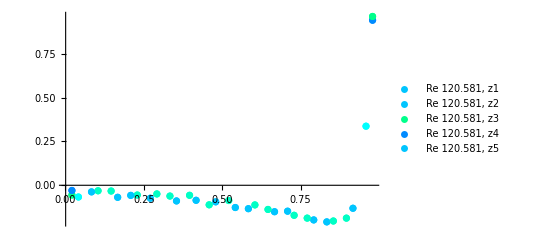

```mathematica
ldcp=ListPlot[{#}&/@ldd, PlotRange->All, PlotStyle->hues, PlotLegends->Table["Re "<>ToString[rens]<>", z"<>ToString[i], {i, hn}]]
```

```mathematica
ghia10000={
{1, 1}, {0.9766, 0.47221}, {0.9688,0.47783}, {0.9609,0.48070}, 
{0.9531,0.47804}, {0.8516,0.34635}, {0.7344,0.20673},
 {0.6172,0.08344}, {0.5,0.03111},{0.4531,-0.07540}, 
{0.2813,-0.23186},{0.1719,-0.32709}, {0.1016,-0.38000}, {0.0703,-0.41657},
{0.0625, -0.42537}, {0.0547,-0.42735}, {0,0}
};
```

```mathematica
ghia10000p=ListPlot[ghia10000, PlotStyle->Black, PlotMarkers->▲, PlotLegends->{"Re 10000 (Ghia et al.)"}];
```

```mathematica
ghia1000={
{1, 1}, {0.9766, 0.65928}, {0.9688,0.57492}, {0.9609,0.511117}, 
{0.9531,0.46604}, {0.8516,0.33304}, {0.7344,0.18719},
 {0.6172,0.05702}, {0.5,-0.06080},{0.4531,-0.10648}, 
{0.2813,-0.27805},{0.1719,-0.38289}, {0.1016,-0.29730}, {0.0703,-0.2222},
{0.0625, -0.20196}, {0.0547,-0.18109}, {0,0}
};
```

```mathematica
ghia1000p=ListPlot[ghia1000, PlotStyle->Black, PlotMarkers->▲, PlotLegends->{"Re 1000 (Ghia et al.)"}];
```

```mathematica
ghia100={
{1, 1}, {0.9766, 0.84123}, {0.9688,0.78871}, {0.9609,0.73722}, 
{0.9531,0.68717}, {0.8516,0.23151}, {0.7344,0.00332},
 {0.6172,-0.13641}, {0.5,-0.20581},{0.4531,-0.21090}, 
{0.2813,-0.15662},{0.1719,-0.10150}, {0.1016,-0.06434}, {0.0703,-0.04775},
{0,0}
};
```

```mathematica
ghia100p=ListPlot[ghia100, PlotStyle->Black, PlotMarkers->■, PlotLegends->{"Re 100 (Ghia et al.)"}];
```

```mathematica
ghia100ip=Plot[Interpolation[ghia100, Method->"Spline"][x], {x, 0.0, 1}, PlotStyle->{Dashed, Lighter[Blue, 0.5]}, PlotLegends->{"Re 100 (Ghia et al.)"}, PlotRange->All];
ghia1000ip=Plot[Interpolation[ghia1000, Method->"Spline"][x], {x, 0.0, 1}, PlotStyle->{Dashed, Lighter[Cyan, 0.5]}, PlotLegends->{"Re 1000 (Ghia et al.)"}, PlotRange->All];ghia10000ip=Plot[Interpolation[ghia10000, Method->"Spline"][x], {x, 0.0, 1}, PlotStyle->{Dashed, Lighter[Green, 0.5]}, PlotLegends->{"Re 10000 (Ghia et al.)"}, PlotRange->All];
```

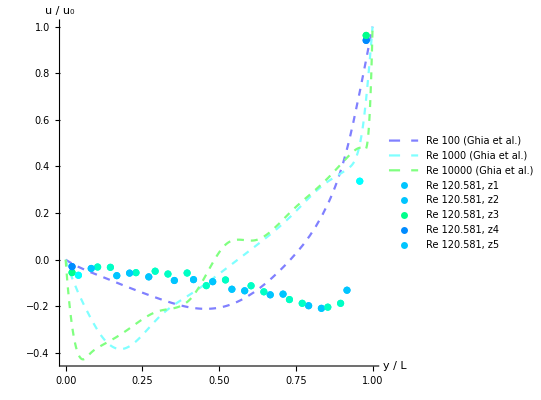

```mathematica
bpl=Show[ghia100ip, ghia1000ip, ghia10000ip,ldcp, AspectRatio->1, AxesLabel->{"y / L", "u / u_0"}, PlotRange->All]
```

```mathematica
Export["~/Dropbox/lidbench.pdf", bpl]
```

~/Dropbox/lidbench.pdf